# David Meretzky Helmholtz

## Parameters

```mathematica
(**)
```

## Geometry

```mathematica
nodes = {};
elements = {};
columns = 
n = 0;
For[i = 0, i ≤20,  i++, 
For[j =0, j ≤ 10, j++, 
n++;
node = {};
AppendTo[node, n];
AppendTo[node,i];
AppendTo[node, Mod[j,11]];
AppendTo[nodes,node];
];
];


n = 0;
For[i = 0, i ≤ 19, i++, 
For[k = 1, k ≤ 10, k++, 
For[j = 1, j ≤ 2,j ++, 
n++;
element = {};

AppendTo[element, n];

If[OddQ[j], 
AppendTo[element, (i*11)+k];
AppendTo[element,(i*11)+k + 11]; 
AppendTo[element, (i*11)+k + 12]; 
];

If[EvenQ[j], 
AppendTo[element,(i*11)+k];
AppendTo[element, (i*11)+k+12]; 
AppendTo[element, (i*11)+k+1]; 
];

AppendTo[elements, element];

];(* end of even odd counter*)
]; (* end of iterator over rows *)
]; (* end of iterator over columns *)
```

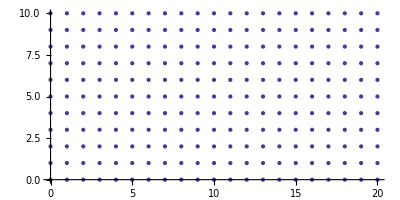

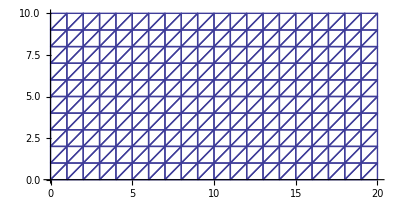

```mathematica
el= {};
For[i = 1, i ≤ Length[elements], i++,


node = nodes[[elements[[i,2;;4]],2;;3]];
 AppendTo[node,nodes[[elements[[i,2;;4]],2;;3]][[1]]];
AppendTo[el,node];
];

ListPlot[nodes[[1;;Length[nodes],2;;3]], AspectRatio->Automatic]
ListLinePlot[el, PlotStyle->Hue[.67, .6, .6], AspectRatio->Automatic]
```

## Formation of Vandermond Matrix and Polynomails

```mathematica
vand = {{1,0,0},{1,1,0},{1,0,1}};
units = {{1,0,0},{0,1,0},{0,0,1}};
MatrixForm[vand];

pol1[x_ , y_] :=LinearSolve[vand, units[[1]]].{1,x,y};
pol2[x_ , y_] :=LinearSolve[vand, units[[2]]].{1,x,y};
pol3[x_ , y_] :=LinearSolve[vand, units[[3]]].{1,x,y};

polys = {pol1,pol2,pol3};

grads = {{D[pol1[x,y],x],D[pol1[x,y],y]},
{D[pol2[x,y],x],D[pol2[x,y],y]},
{D[pol3[x,y],x],D[pol3[x,y],y]}};

Φ[x_, y_] := {.25*(1+x)*(1-y),.5*(1+y)};
```

## Analysis, K and M matricies

```mathematica
knByn = 0 *IdentityMatrix[Length[nodes]];
mnByn = 0 *IdentityMatrix[Length[nodes]];
For[i = 1, i ≤ Length[elements], ++i, 
coords = {{α,β},{γ,δ},{μ,ν}} = nodes[[elements[[i,2;;4]],2;;3]];

element = elements[[i]];

jacobianMatrix = Abs[Det[{{γ-α,μ-α},{δ-β,ν-β}}]];

xpts = {-1/Sqrt[3],1/Sqrt[3]};
ypts = {-1/Sqrt[3],1/Sqrt[3]};

For[j = 1, j ≤ 3,j++, 
nj = element[[2;;4]][[j]];
For[k = 1, k ≤ 3, k++,
nk = element[[2;;4]][[k]];

knByn[[nj,nk]] +=(1/8)*∑_(l=1)^2 ∑_(m=1)^2 (grads[[j]].grads[[k]])*jacobianMatrix;

mnByn[[nj,nk]] +=(1/8)*∑_(l=1)^2 ∑_(m=1)^2 polys[[j]][Φ[xpts[[l]],ypts[[m]]][[1]],Φ[xpts[[l]],ypts[[m]]][[2]]]*polys[[k]][Φ[xpts[[l]],ypts[[m]]][[1]],Φ[xpts[[l]],ypts[[m]]][[2]]]
*jacobianMatrix     (* end of summation *)


];   (* end of first iterator over polynomial gradients *)

];   (* end of second iterator over polynomial gradients *)
];  (* end of iterator over elements*)
```

## Dirichlet Boundary Conditions

```mathematica
uvect=ConstantArray[0,231];

uvect[[1]] = 1;

knByn[[1]]=uvect;
mnByn[[1]]=uvect;
```

## Solving the Eigensystem

```mathematica
invmnByn=Inverse[mnByn];
eigenVectors = Eigenvectors[knByn.invmnByn];
eigenValues = Eigenvalues[knByn.invmnByn];
```

## Post Processing making final polynomials

```mathematica
frames = {};

For[j = 1, j ≤ 231, ++j, 
frame = {};
For[i = 1, i ≤ 400, i ++, 

polys = {pol1[centerx,centery], pol2[centerx,centery],pol3[centerx,centery]};


If[OddQ[i],
centerx = nodes[[elements[[i,2;;4]],2;;3]][[1,1]] + .7;
centery = nodes[[elements[[i,2;;4]],2;;3]][[1,2]] + .3;
];
If[EvenQ[i],
centerx = nodes[[elements[[i,2;;4]],2;;3]][[1,1]] + .3;
centery = nodes[[elements[[i,2;;4]],2;;3]][[1,2]] + .7;
];

polynomial = 
eigenVectors[[j,elements[[i,2]]]]*polys[[1]]+
eigenVectors[[j,elements[[i,3]]]]*polys[[2]]+
eigenVectors[[j,elements[[i,4]]]]*polys[[3]];


AppendTo[frame,{centerx,centery,polynomial}];
];(* end of loop over elements    400 *)
AppendTo[frames, frame];
]; (* end of loop over eigenvectors    231  *)
```

## Visualization

```mathematica
ListPlot3D[frames[[1]], PlotRange->All]
ListPlot3D[frames[[20]], PlotRange->All]
ListPlot3D[frames[[40]], PlotRange->All]
ListPlot3D[frames[[100]], PlotRange->All]
ListPlot3D[frames[[200]], PlotRange->All]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»